## Investigation of the Fuel Cell Equations

In the literature cm is usually used as the length scale. Here SI units are used which means that a factor 10^2 is sometimes used to compensate for this.

```mathematica
ucell:=Enernst-uact-uOhmic-ucon
```

Nernst equation

```mathematica
Enernst:=dG/(2 F)+dS/(2 F)(T-Tref)+(R T)/(2 F)Log[(Ph2 √Po2)/P0]
```

```mathematica
uact=-(ksi1+ksi2 T + ksi3 T Log[Co2]+ksi4 T Log[ifc]);
```

```mathematica
uOhmic:=(rhoM l 10^2)/(A 10^4)ifc
```

```mathematica
rhoM:=(181.6 (1+0.03(ifc/(A 10^4))+0.062(T/303)^2(ifc/(A 10^4))^2.5))/(psi-0.634-3(ifc/(A 10^4))E^(4.18((T-303)/T)))
```

```mathematica
Co2:=Po2/(5.08 10^6 E^(-498/T))
```

```mathematica
ucon:=-B Log[1-J/Jmax]
```

Approximate expression for Log[1-x] to avoid infinite derivative.

```mathematica
LogA1[x_]:=-(1.3 x)/(1-(0.93x)^4)
```

```mathematica
uconA:=-B LogA1[J/Jmax]
```

Here is is tested without

```mathematica
ucon:=-B Log[1-J/Jmax]
```

```mathematica
ksi2:=0.00286+0.0002 Log[A 10^4]+4.3 10^-5 Log[Ch2]
```

```mathematica
dS=.85 10^-3 2F
```

164.025

```mathematica
psi=23.;T=300;
```

```mathematica
F=96485.33212;
R=8.314;
Tref=298.15;
dG=228000.6;
P0=1;
```

```mathematica
n=48;
T=323;
A=62.5 10^-4;
l=25 10^-6;
Ph2=1.476;
Po2=0.2095;
B=0.15;
Rc=0.0003;
ksi1=-.948;ksi3=7.22 10^-5;ksi4=-1.0615 10^-4;
psi=23;
Jmax=672 10^-3 10^4;
Jn=22 10^-3 10^4;
Imax=42;
```

```mathematica
J=ifc/A
```

160. ifc

```mathematica
160. ifc
```

160. ifc

```mathematica
Ch2=1;
```

```mathematica
rhoM
```

(181.6 (1+0.00048 ifc+2.28145×10^-6 ifc^2.5))/(22.366-0.0621794 ifc)

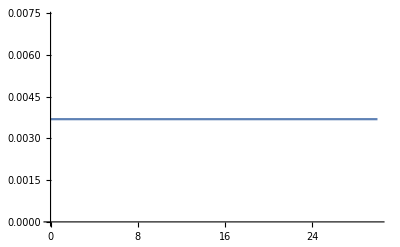

```mathematica
Plot[ksi2,{ifc,0,30}]
```

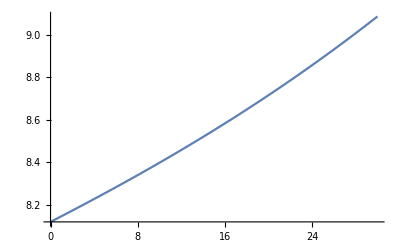

```mathematica
Plot[rhoM,{ifc,0,30}]
```

Comparison with the aprocimate expression for uconA

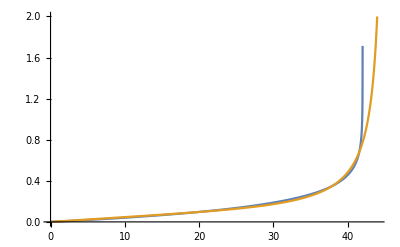

```mathematica
Plot[{ucon,uconA},{ifc,0,44},PlotRange->{0,2}]
```

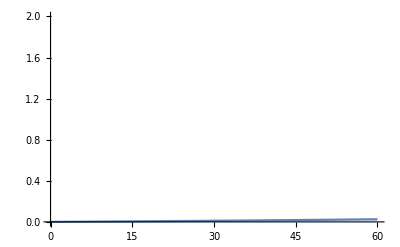

```mathematica
Plot[uOhmic,{ifc,0,60},PlotRange->{0,2}]
```

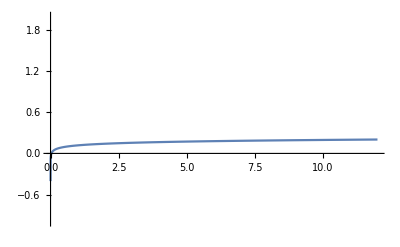

```mathematica
Plot[uact,{ifc,0,12},PlotRange->{-1,2}]
```

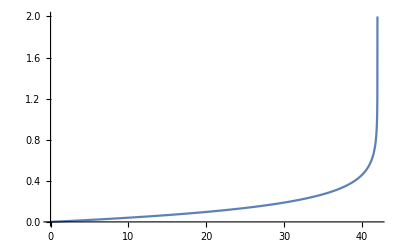

```mathematica
Plot[{ucon},{ifc,0,60},PlotRange->{0,2}]
```

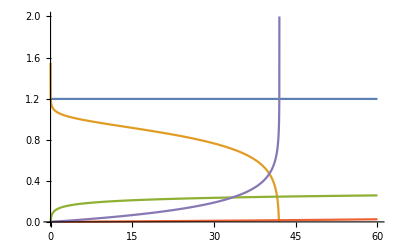

```mathematica
Plot[{Enernst,ucell,uact,uOhmic,ucon},{ifc,0,60}, PlotRange->{0,2}]
```